```mathematica
Quit[];
```

```mathematica
ListPercentagePlot[M_?NumericQ,Γ_?NumericQ,Δ_?NumericQ]:=(ListDat=({#[[1]],(4π)/M^2#[[2]],#[[3]]}&)/@(Take[#,3]&)/@Drop[Import[StringForm["C:/Users/hypercube256/Desktop/Study/Higgs and SMEFT/Detectability Estimation/``GeV_``GeV_``GeV.csv",M,Γ,Δ]//ToString],1];
Show[ListDensityPlot[ListDat,PlotRange->{10^-8,10^-1},PlotLegends->Placed[BarLegend[{Automatic,{10^-8,10^-1}},Ticks->Table[{10^i,ToString[Superscript["10",i],StandardForm]},{i,-8,-1,1}],ColorFunctionScaling->True],{1,0.55}],PlotRange->All,FrameLabel->{Style["m_ϕ (GeV)",16],Style["g^2/4πM^2",16]},ScalingFunctions->{"Linear","Log","Log"},ColorFunction->"SunsetColors",LabelStyle->{Black,12,FontFamily->"Times New Roman"}],ListContourPlot[ListDat,Contours->{{0.0001,Dashed},{0.01,Dashed}},ScalingFunctions->{"Linear","Log"},ContourShading->None,PlotRange->All],
RegionPlot[ c √Max[M^2-4 m^2,0]≥4Γ,{m,M/2-Γ,M/2+Γ},{c,1/100,4},ScalingFunctions->{"Linear","Log","Log"},BoundaryStyle->None,PlotStyle->White,MaxRecursion->10]])
```

```mathematica
ListPercentagePlot[1000,100,0]
```

-Graphics-

```mathematica
ListPercentagePlot[1000,100,10]
```

-Graphics-

```mathematica
ListPercentagePlot[1000,100,20]
```

-Graphics-

```mathematica
ListPercentagePlot[1000,100,50]
```

-Graphics-

```mathematica
ScalarF0[m_,s_]:=If[s==0,-2Log[m],If[s==4 m^2,2-2Log[m],2-2Log[m]-(2 √(4 m^2-s))/(√s)ArcTan[(√s)/(√(4 m^2-s))]]] ;
ScalarFPrime0[m_,s_]:=If[s==4 m^2,-1/(4 m^2),-1/s+(4 m^2)/(√(4 m^2-s) s^(3/2))ArcTan[(√s)/(√(4 m^2-s))]];
PropagatorScalar[s_,M_,m_,c_,Γ_]:=1/(s-M^2+ⅈ×M×Γ+c×(ScalarF0[m,s]-ScalarF0[m,M^2]-(s-M^2)Re[ScalarFPrime0[m,M^2]]));
NWA[A_?NumericQ,B_?NumericQ,Z_?NumericQ,s_?NumericQ]:=Z/((s-A)^2+B^2);
```

```mathematica
BestFit[M_,m_,c_,Γ_]:=FindMinimum[Sum[Abs[Abs[PropagatorScalar[p^2,M,m,c,Γ]]^2-NWA[A,B,Z,p^2]]^2,{p,M-2Γ,M+2Γ,Γ/400}],{{A,M^2},{B,M×Γ},{Z,1}}];
SqSum[M_,m_,c_,Γ_]:=Sum[Abs[PropagatorScalar[p^2,M,m,c,Γ]]^4,{p,M-2Γ,M+2Γ,Γ/400}];
Lumrat[M_,m_,α_,Γ_]:=BestFit[M,m,(M^2 α)/(4π),Γ][[1]]/SqSum[M,m,(M^2 α)/(4π),Γ];
PlotRes[M_,m_,α_,Γ_]:=Plot[{Abs[PropagatorScalar[p^2,M,m,(M^2 α)/(4π),Γ]]^2,NWA[A,B,Z,p^2]/.{BestFit[M,m,(M^2 α)/(4π),Γ][[2]]}},{p,M-2Γ,M+2Γ}];
```

```mathematica
Lumrat[1000,480,0.514,100]
```

0.0100066

```mathematica
Lumrat[1000,500,0.445,100]
```

0.0100255

```mathematica
Lumrat[1000,510,0.661,100]
```

0.0100117

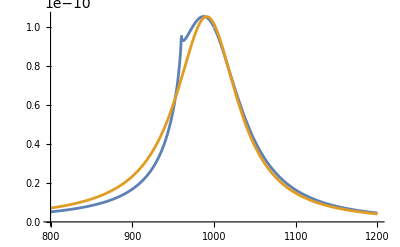

```mathematica
PlotRes[1000,480,0.514,100]
```

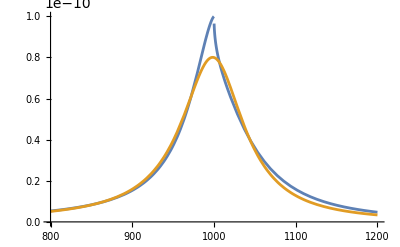

```mathematica
PlotRes[1000,500,0.445,100]
```

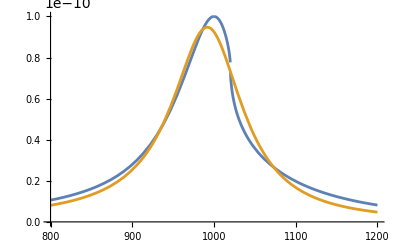

```mathematica
PlotRes[1000,510,0.661,100]
```